## q parameter thru thin lens and then propagate for the focal length

(1-d/f | d
-1/f | 1)

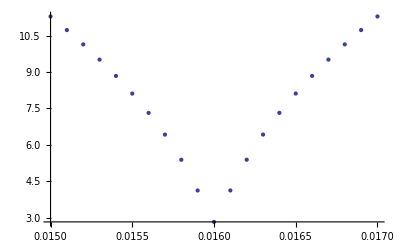

```mathematica
Clear["Global`*"]
kHz=10^3;
nm=10^-9;
mm=10^-3;
um=10^-6;
cm=10^-2;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λ=775nm;
fl=16mm;
waist1=1400um;
mat={{1,d},{0,1}}.{{1,0},{-1/f,1}};
%//MatrixForm
{{aa,bb},{cc,dd}}=mat;


dat=Reap[Do[
q1=1/(-I λ/(π w1^2));
q2=(aa q1+bb)/(cc q1+dd)/.d->f+Δ/.f->fl/.w1->waist1;
Sow[{fl+Δ,1. Re[w2]/um/.Solve[1/q2==-I λ/(π w2^2),w2][[2]]}]

,{Δ,-1mm,1mm, .1mm}]][[2,1]];

ListPlot[dat]
```